# Finding a Parametrization for the Rough Dielectric Surface Simulation

We wrote a program that is capable of generating or loading a microsurface and ray-tracing that surface using a very large amount of rays (several hundred millions), thus obtaining the distribution of outgoing directions after 1 or more scattering events (up to 4).
We gathered the outgoing lobes for different parameters of the surface:
	• Angle of incidence θ_s
	• Roughness α_s
	• Albedo ρ_s

We then performed a fitting of the simulated data using a modified cosine lobel model that uses non-uniform scaling and a local tangent space.
The matrix M allows to transform from local lobe space to surface space:

	A=(σ_t T
σ_b B
R(θ_l))
	ω_w= (ω_l ·A)/(|ω_l ·A|)
	ω_l= (ω_w· A^-1)/(|ω_w ·A^-1|)
	
ω_l is the local lobe-space unit vector
ω_w is the surface-space unit vector after renormalization
R(θ_l) is the lobe’s principal axis (usually, the reflected incoming direction). It’s defined by one of the parameters of the lobe model θ_l
T, B are the complementary vectors forming an orthonormal basis with N
σ_n is a non-uniform scaling factor along the lobe’s principal direction and another one of the parameters of the lobe model

#### Lobe Intensity in Local-Space, Given Two Directions in Surface-Space

Once in local lobe-space, the intensity of the lobe is given by:

	f(ω_o,ω_i,α,σ,m) = σ [(1-m) + m G(ω_o·Z,α) G(ω_i·Z,α)] N( ω_i, α )
	
	G(θ,α) = Piecewise[{{(3.535 a + 2.181 a^2)/(1.0 + 2.276 a + 2.577 a^2), a(θ,α) < 1.6}, {1, otherwise}}]
	a(θ,α) = (√(1+(η(α))/2))/(tan(θ))
	N( ω_i, α ) =  (2+η(α))/π [(ω_i ·A^-1)/(|ω_i ·A^-1|).Z]^(η(α))	
	η(α)= 2^(10(1-α))-1
	
	ω_o is the outgoing view direction in surface space
	ω_i is the incoming light direction in surface space
	σ is the global scale factor
	α is the lobe’s roughness
	m is the masking importance factor in [0,1] that allows to bypass the masking term (m=0) completely.
	G(θ,α) is the masking term for the Phong model
	N( ω_i, α ) defines the cosine lobe’s intensity using roughness α, angle from local normal axis and global scale
	η(α) defines the exponent based on the surface’s roughness α (notice the -1 in the end that allows use to have a 0 exponent to make constant lobes)
	Z is the unit Z-up vector (0,0,1)

```mathematica
Lobe Intensity in Surface-Space
```

We need to quickly find the length of the surface-space vector ω_w when transformed from local lobe-space to suface-space:

	L = |ω_l·A|

We know that for an unscaled lobe direction ω_l we get the scaled version ω_s:

	ω_s = ω_l (1 | 0 | 0
0 | 1 | 0
0 | 0 | σ_n)
	L = |ω_s|
	
And the unit surface-space direction is:

	ω_w= ω_s/L

Now, if we write:

	ω_l =ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)

Since |ω_l| = 1 :

	|ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)|=1

This lets us solve for L:

	L(σ_n) = 1/(√(1+[ω_w · Z]^2 (1/σ_n^2-1)))

So in the end, we can estimate the final lobe size in surface-space as:

	f_w(ω_o,ω_i,α,σ,σ_n,m) = L(σ_n) f(ω_o,ω_i,α,σ,m)


Building the Local Tangent Space

Knowing the incoming light direction ω_i (pointing away from the surface) and assuming it’s pointing upward, we can easily setup T_0 as:

	T_0 = ((0,1,0) × ω_i)/(|(0,1,0) × ω_i|)
	
This gives us a flat base to orient our cosine lobe:

	R(θ) = cos(θ) (0,0,1) sin(θ) T_0

From R(θ) it’s easy to retrieve T and B as:

	T = (R(θ) × (0,0,1))/(|R(θ) × (0,0,1)|)
	B = T × R(θ)

## Resulting Model

After fitting each parameter one after another, we noticed that:
	• Incident light angle θ has no effect on fitted lobe, assuming we ignore the backscattering that is visible at highly grazing angles and that would be better fitted using maybe a GGX lobe that features a nice backscatter property.
	• Final masking importance m is 0 after all
	• There is only a dependency on albedo ρ for the scale factor (that was expected) and it is proportional to ρ^2 which was also expected.
	
Finally, we obtain the following analytical model for 2nd order scattering of a rough diffuse surface:

	f_2(ω_o,α,ρ) = σ_2(ρ) μ^(η(α))
	
	μ = ω_o·Z
	η(α) = 0.7782894918463 + 0.1683172467667511 α		the fitted exponent with a dependency on roughness alone
	σ_2( α, ρ ) = k(ρ) [2.32484 α-2.75021 α^2+1.01261 α^3]	the fitted scale factor with a dependency on albedo and roughness
	k_2(ρ) = ρ^2								the factor applied to scale that will give use the expected color saturation
	
The flattening factor along the main lobe direction Z is the most expensive to compute:
	a(α) = 0.697462 - 0.479278 (1-α)
	b(α) = 0.287646 - 0.293594 (1-α)
	c(α) = 5.69744 + 6.61321 (1-α)
	σ_n(μ, α) = a(α) + b(α) e^(-c(α)  μ)

An alternate model is possible using a power of 2:
	c'(α) = 8.21968 + 9.54087 (1-α)
	σ_n'(μ, α) = a(α) + b(α) 2^(-c'(α)  μ)
	
So the world-space intensity of the fitted lobe is obtained by multiplying the lobe-space intensity with the scale factor:

	f_w(ω_o,α,ρ) = L(μ,σ_n(μ, α)) f_2(ω_o,α,ρ)
	
	L(μ, σ_n(μ, α)) = 1/(√(1+μ^2 (1/(σ_n(μ,α))^2-1)))

## Additional Scaling for 3rd Order Lobes

Using the same analytical model for 3rd order scattering lobes but letting the σ parameter free for new evaluation, we obtain a pretty good fit for a new σ_3(α, ρ)

	σ_3(α, ρ) = k_3(ρ) [-0.00602406+0.252628 α+0.390207 α^2-0.382049 α^3]	the fitted scale factor with a dependency on albedo and roughness
	k_3(ρ) = ρ^3											the factor applied to scale that will give use the expected color saturation

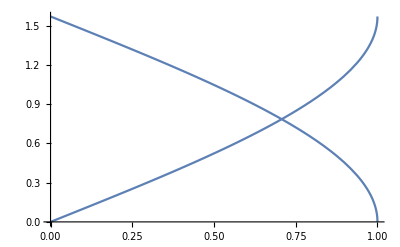

{0.,0.451027,0.643501,0.795399,0.927295,1.0472,1.15928,1.2661,1.36944,1.47063,1.5708}

```mathematica
Show[
Plot[ArcCos[x],{x,0,1}],
Plot[ArcSin[x],{x,0,1}]
]
Table[N[ArcCos[1-i/10]],{i,0,10}]
```

1/N=∫_θ_0^θ_1 sin(θ)ⅆθ = cos(θ_1) - cos(θ_0)

Si je pose θ_0 = 0 (condition initiale au pôle) :
cos( 0 ) - cos( θ_1 ) = 1/N → θ_1 = cos^-1( 1 - 1/N )

Si je continue et que je pose θ_0 = cos^-1( 1 - 1/N ) alors :
cos( θ_0 ) - cos( θ_1 ) = 1 - 1/N -  cos( θ_1 ) = 1/N → θ_1 = cos^-1( 1 - 2/N )

etc.

Set::write: Tag Integrate in ∫_a b Sin[θ] ⅆ θ is Protected.

Set::write: Tag Times in 1/N is Protected.

Cos[a]-Cos[b]

# Parametrization

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse

OpenRead::noopen: Cannot open "results_order2_slice0.bin".

$Failed

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

OpenRead::noopen: Cannot open "results_order2_slice1.bin".

$Failed

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

OpenRead::noopen: Cannot open "results_order2_slice2.bin".

$Failed

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

OpenRead::noopen: Cannot open "results_order2_slice3.bin".

$Failed

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 5 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 5 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 5 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

Part::partw: Part 5 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
table0[[10,20]]
```

BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦200⟧

Parametrizing Theta

```mathematica
paramsTheta0 = Table[table0[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta1 = Table[table1[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta2 = Table[table2[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta3 = Table[table3[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsTheta0]
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

($Failed⟦1⟧ | Real64 | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]
BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}] | BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}])

```mathematica
Show[ListPlot3D[paramsTheta0,{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta1,{ColorFunction->RGBColor[0,1,0],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta2,{ColorFunction->RGBColor[0,0,1],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta3,{ColorFunction->RGBColor[1,1,0],PlotRange->{0,π/2}}] ]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

Fitting Lobe Roughness

```mathematica
paramsAlpha0 = Table[table0[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha1 = Table[table1[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha2 = Table[table2[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha3 = Table[table3[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsAlpha0]
```

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

($Failed⟦2⟧ | Real64 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100
101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120
121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140
141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160
161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180
181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200)

```mathematica
roughness2exponent[α_] := 2^(10*(1-α))-1
roughness2exponent[0.95913]
```

0.327489

```mathematica
ListPlot3D[roughness2exponent[paramsAlpha0],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[roughness2exponent[paramsAlpha1],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[roughness2exponent[paramsAlpha2],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[roughness2exponent[paramsAlpha3],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

It would seem that, ignoring the last 2 or 3 rows of each array, we have quite a uniform roughness.
Averaging roughnesses we obtain:

```mathematica
avgAlpha0 = Sum[paramsAlpha0[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgAlpha1 = Sum[paramsAlpha1[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgAlpha2 = Sum[paramsAlpha2[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgAlpha3 = Sum[paramsAlpha3[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
```

1/140 (9867+Real64+$Failed⟦2⟧)

1/140 (9867+Real64+$Failed⟦2⟧)

1/140 (9867+Real64+$Failed⟦2⟧)

«1 more identical outputs»

```mathematica
avgExponent0=roughness2exponent[avgAlpha0]
avgExponent1=roughness2exponent[avgAlpha1]
avgExponent2=roughness2exponent[avgAlpha2]
avgExponent3=roughness2exponent[avgAlpha3]
```

-1+2^(10 (1+1/140 (-9867-Real64-$Failed⟦2⟧)))

-1+2^(10 (1+1/140 (-9867-Real64-$Failed⟦2⟧)))

-1+2^(10 (1+1/140 (-9867-Real64-$Failed⟦2⟧)))

«1 more identical outputs»

So we could use an average exponent of 0.7, maybe 0.5 so we could simply take the square root of the cosine term?

Matching Lobe Global Scale

```mathematica
paramsScale0 = Table[table0[[j]][[i]][[3]],{j,1,resY},{i,1,resX}]
paramsScale1 = Table[table1[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale2 = Table[table2[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale3 = Table[table3[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
```

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{$Failed⟦3⟧,Real64,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦121⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦122⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦123⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦124⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦125⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦126⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦127⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦128⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦129⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦130⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦131⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦132⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦133⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦134⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦135⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦136⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦137⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦138⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦139⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦140⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦141⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦142⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦143⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦144⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦145⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦146⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦147⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦148⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦149⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦150⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦151⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦152⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦153⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦154⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦155⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦156⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦157⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦158⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦159⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦160⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦161⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦162⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦163⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦164⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦165⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦166⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦167⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦168⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦169⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦170⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦171⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦172⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦173⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦174⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦175⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦176⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦177⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦178⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦179⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦180⟧⟦3⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦181⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦182⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦183⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦184⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦185⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦186⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦187⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦188⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦189⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦190⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦191⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦192⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦193⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦194⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦195⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦196⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦197⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦198⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦199⟧⟦3⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦200⟧⟦3⟧}}

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 3 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
ListPlot3D[paramsScale0,{ PlotRange->{0,0.7},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale1,{ PlotRange->{0,0.4},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale2,{ PlotRange->{0,0.1},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale3,{ PlotRange->{0,0.025},AxesLabel->{"θ","ρ"}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

Matching Lobe Flattening Factor ==> FIRST PARAMETER MATCHED!

```mathematica
paramsFlat0 = Table[table0[[j]][[i]][[4]],{j,1,resY},{i,1,resX}]
paramsFlat1 = Table[table1[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat2 = Table[table2[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat3 = Table[table3[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
```

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{$Failed⟦4⟧,Real64,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦121⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦122⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦123⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦124⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦125⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦126⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦127⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦128⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦129⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦130⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦131⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦132⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦133⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦134⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦135⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦136⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦137⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦138⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦139⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦140⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦141⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦142⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦143⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦144⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦145⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦146⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦147⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦148⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦149⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦150⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦151⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦152⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦153⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦154⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦155⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦156⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦157⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦158⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦159⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦160⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦161⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦162⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦163⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦164⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦165⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦166⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦167⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦168⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦169⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦170⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦171⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦172⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦173⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦174⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦175⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦176⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦177⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦178⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦179⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦180⟧⟦4⟧},{BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦181⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦182⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦183⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦184⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦185⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦186⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦187⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦188⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦189⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦190⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦191⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦192⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦193⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦194⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦195⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦196⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦197⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦198⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦199⟧⟦4⟧,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦200⟧⟦4⟧}}

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ does not exist.

Part::partw: Part 4 of BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
ListPlot3D[paramsFlat0,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsFlat1,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat2,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat3,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

We see that for albedo 1 and 0.75, the shape is pretty similar and that for lower albedos the change was neglected and is always 1.
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in ρ is from index 1 to about 6.

```mathematica
test=Table[{(i-1)/(resX-1),  paramsFlat0[[1]][[i]]},{i,1,resX}];
ListPlot[test];
valuesSn=Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,6}];
Show[Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

-Graphics-

```mathematica
modelSn=a+b*Exp[-c * u];
fittingSn = Table[FindFit[ valuesSn[[j]],modelSn,{a,b,c},u ],{j,1,6}];
MatrixForm[fittingSn]
MatrixForm[modelSn/.fittingSn]
Show[Table[Plot[modelSn/.fittingSn[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/6]],{j,1,6}],
Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

(FindFit[{{1,$Failed⟦4⟧},{Cos[π/38],Real64},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]
FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]
FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]
FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]
FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]
FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u])

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a+b ⅇ^(-c u)/.{FindFit[{{1,$Failed⟦4⟧},{Cos[π/38],Real64},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u],FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u],FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u],FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u],FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u],FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]}

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b, {« 1 »}, 0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b, {« 1 »}, 0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + « 1 », « 1 », « 24 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

#### Matching Parameters

Now that we have a bunch of nice expressions for representing f(cos(θ)), we need to find tendencies in the fitted parameters a, b and c.

```mathematica
fa = Table[{(j-1)/9,a/.fittingSn[[j]]}, {j,1,6}];
fb = Table[{(j-1)/9,b/.fittingSn[[j]]}, {j,1,6}];
fc= Table[{(j-1)/9,c/.fittingSn[[j]]}, {j,1,6}];
mfa = LinearModelFit[fa,x,x];
mfb = LinearModelFit[fb,x,x];
mfc = LinearModelFit[fc,x,x];
Normal[mfa]
Normal[mfb]
Normal[mfc]
Show[ListPlot[fa,PlotRange->{0,1}],Plot[mfa[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fb,PlotRange->{0,1}],Plot[mfb[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fc,PlotRange->{0,10}],Plot[mfc[x],{x,0,1}],PlotRange->All]
```

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0,a/.FindFit[{{1,$Failed⟦4⟧},{Cos[π/38],Real64},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/9,a/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{2/9,a/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/3,a/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{4/9,a/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{5/9,a/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]}},x,x]

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0,b/.FindFit[{{1,$Failed⟦4⟧},{Cos[π/38],Real64},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/9,b/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{2/9,b/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/3,b/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{4/9,b/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{5/9,b/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]}},x,x]

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0,c/.FindFit[{{1,$Failed⟦4⟧},{Cos[π/38],Real64},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦3⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦4⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦5⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦6⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦7⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦8⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦9⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦10⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦11⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦12⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦13⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦14⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦15⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦16⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦17⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦18⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦19⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦20⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/9,c/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦21⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦22⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦23⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦24⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦25⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦26⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦27⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦28⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦29⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦30⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦31⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦32⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦33⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦34⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦35⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦36⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦37⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦38⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦39⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦40⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{2/9,c/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦41⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦42⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦43⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦44⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦45⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦46⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦47⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦48⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦49⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦50⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦51⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦52⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦53⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦54⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦55⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦56⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦57⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦58⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦59⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦60⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{1/3,c/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦61⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦62⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦63⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦64⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦65⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦66⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦67⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦68⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦69⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦70⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦71⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦72⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦73⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦74⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦75⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦76⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦77⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦78⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦79⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦80⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{4/9,c/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦81⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦82⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦83⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦84⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦85⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦86⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦87⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦88⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦89⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦90⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦91⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦92⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦93⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦94⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦95⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦96⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦97⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦98⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦99⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦100⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]},{5/9,c/.FindFit[{{1,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦101⟧⟦4⟧},{Cos[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦102⟧⟦4⟧},{Cos[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦103⟧⟦4⟧},{Cos[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦104⟧⟦4⟧},{Cos[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦105⟧⟦4⟧},{Cos[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦106⟧⟦4⟧},{Cos[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦107⟧⟦4⟧},{Cos[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦108⟧⟦4⟧},{Cos[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦109⟧⟦4⟧},{Cos[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦110⟧⟦4⟧},{Sin[(9 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦111⟧⟦4⟧},{Sin[(4 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦112⟧⟦4⟧},{Sin[(7 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦113⟧⟦4⟧},{Sin[(3 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦114⟧⟦4⟧},{Sin[(5 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦115⟧⟦4⟧},{Sin[(2 π)/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦116⟧⟦4⟧},{Sin[(3 π)/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦117⟧⟦4⟧},{Sin[π/19],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦118⟧⟦4⟧},{Sin[π/38],BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦119⟧⟦4⟧},{0,BinaryReadList[$Failed,{Real64,Real64,Real64,Real64,Real64}]⟦120⟧⟦4⟧}},a+b ⅇ^(-c u),{a,b,c},u]}},x,x]

FindFit::nrlnum: The function value {1.36788  - 1.\ $Failed ⟦ 4 ⟧, 1.36914  - 1.\ "Real64", 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 3 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 4 ⟧ ⟦ 4 ⟧, 1.38836  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 5 ⟧ ⟦ 4 ⟧, « 11 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 17 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 18 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 19 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 20 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, $Failed ⟦ 4 ⟧}, {Cos[π/38], "Real64"}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 3 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 4 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 5 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 6 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 7 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 8 ⟧ ⟦ 4 ⟧}, {Cos[4\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 9 ⟧ ⟦ 4 ⟧}, {Cos[9\ π/38], « 1 »}, {Sin[9\ π/38], « 1 »}, « 1 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 13 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 14 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 15 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 16 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 17 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 18 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 19 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 20 ⟧ ⟦ 4 ⟧}}, a + b\ « 1 », « 1 », u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 21 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 22 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 23 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 24 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 37 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 38 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 39 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 40 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 21 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 22 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 23 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 24 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 25 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 26 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 27 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 28 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 33 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 34 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 35 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 36 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 37 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 38 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 39 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 40 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {1.36788  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 41 ⟧ ⟦ 4 ⟧, 1.36914  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 42 ⟧ ⟦ 4 ⟧, 1.37293  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 43 ⟧ ⟦ 4 ⟧, 1.37931  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 44 ⟧ ⟦ 4 ⟧, « 12 », 1.78232  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 57 ⟧ ⟦ 4 ⟧, 1.84824  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 58 ⟧ ⟦ 4 ⟧, 1.92074  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 59 ⟧ ⟦ 4 ⟧, 2.  - 1.\ BinaryReadList[$Failed, {"Real64", "Real64", "Real64", "Real64", "Real64"}] ⟦ 60 ⟧ ⟦ 4 ⟧} is not a list of real numbers with dimensions {20} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1, BinaryReadList[$Failed, {« 5 »}] ⟦ 41 ⟧ ⟦ 4 ⟧}, {Cos[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 42 ⟧ ⟦ 4 ⟧}, {Cos[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 43 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 44 ⟧ ⟦ 4 ⟧}, {Cos[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 45 ⟧ ⟦ 4 ⟧}, {Cos[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 46 ⟧ ⟦ 4 ⟧}, {Cos[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 47 ⟧ ⟦ 4 ⟧}, {Cos[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 48 ⟧ ⟦ 4 ⟧}, « 4 », {Sin[7\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 53 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 54 ⟧ ⟦ 4 ⟧}, {Sin[5\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 55 ⟧ ⟦ 4 ⟧}, {Sin[2\ π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 56 ⟧ ⟦ 4 ⟧}, {Sin[3\ π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 57 ⟧ ⟦ 4 ⟧}, {Sin[π/19], BinaryReadList[$Failed, {« 5 »}] ⟦ 58 ⟧ ⟦ 4 ⟧}, {Sin[π/38], BinaryReadList[$Failed, {« 5 »}] ⟦ 59 ⟧ ⟦ 4 ⟧}, {0, BinaryReadList[$Failed, {« 5 »}] ⟦ 60 ⟧ ⟦ 4 ⟧}}, a + b\ ⅇ^-c\ u, {a, b, c}, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

#### Final Expression

We can now obtain the final expression for the function matching the lobe flattening factor:

a(ρ) = 0.697462 - 0.479278 ρ
b(ρ) = 0.287646 - 0.293594 ρ
c(ρ) = 5.69744 + 6.61321 ρ
μ = cos(θ)
f( μ, ρ ) = a(ρ) + b(ρ) e^(-c(ρ)  μ)

```mathematica
a[ρ_] = 0.697462 - 0.479278 ρ;
b[ρ_] = 0.287646 - 0.293594 ρ;
c[ρ_] = 5.69744 + 6.61321 ρ;
f[ μ_, ρ_] = a[ρ] + b[ρ] Exp[-c[ρ]  μ];

Plot3D[f[μ,ρ],{μ,0,1},{ρ,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","ρ","Lobe Flattening"}]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","ρ"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

Matching Masking Importance

```mathematica
paramsMask0 = Table[table0[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask1 = Table[table1[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask2 = Table[table2[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask3 = Table[table3[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
```

```mathematica
ListPlot3D[paramsMask0,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask1,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask2,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsMask3,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

-Graphics3D-